# Homework 18

## Problem 18.1

This problem provides a demonstration of including friction in the Lagrangian formalism.

A block of mass m =0.35 kg is attached to a massless spring of spring constant k = 15 N/m and rests on a horizontal surface with a coefficient of friction of μ = 0.01. Assume that the friction force is independent of the speed of the block and has a magnitude given by the usual Ffric = μF_N, where F_N is the normal force. Use the modified Lagrange equation to include friction and determine the motion of the block if it is released from rest at x = 0.10 m (assuming the spring is unstretched at x = 0).

Leave everything symbolic at first. We will plug in numbers later.

Hint for defining the friction force: Use the Sign function to make sure the frictional force is always opposing the direction of the velocity. Sign[a] returns +1 if a>0 and -1 if a<0.

```mathematica
Quit[]
```

```mathematica
T=(1/2)*m*xdot^2
U=(1/2)*k*x^2
L=T-U
Ffric = mu*m*g*Sign[-xdot]
```

(m xdot^2)/2

(k x^2)/2

-(k x^2)/2+(m xdot^2)/2

-g m mu Sign[xdot]

### Solutions

```mathematica
L$=-(k x^2)/2+(m xdot^2)/2;
Ffric$=-g m mu Sign[xdot];
If[FullSimplify[Solve[L==L$,k]]=={{}},Print["L is correct."],Print["L is incorrect."]]
If[FullSimplify[Solve[Ffric==Ffric$,g]]=={{}},Print["Ffric is correct."],Print["Ffric is incorrect."]]
```

L is correct.

Ffric is correct.

Now compute the derivatives and make the replacements for later differentiation.

```mathematica
rule={x->x[t],xdot->x'[t]};
dLdx = D[L,x]/.rule
dLdxdot=D[L,xdot]/.rule
Ffric = Ffric/.rule
```

-k x[t]

m x'[t]

-g m mu Sign[x'[t]]

Now define the modified Lagrange equation that includes the friction force.

```mathematica
eq=dLdx+Ffric==D[dLdxdot,t]
```

-g m mu Sign[x'[t]]-k x[t]==m x''[t]

### Solutions

```mathematica
eq$=-g m mu Sign[x'[t]]-k x[t]==m x''[t];
If[FullSimplify[Solve[eq==eq$,m]]=={{}},Print["Your equation is correct."],Print["Your equation is incorrect."]]
```

Your equation is correct.

Plug in numbers, solve, and plot.

{{x→InterpolatingFunction[…]}}

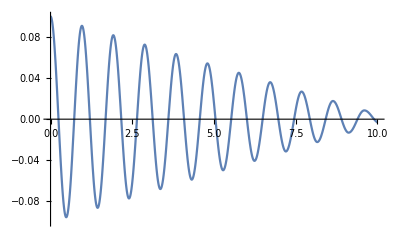

```mathematica
g=9.8;
m=0.35;
k=15;
mu=0.01;

tfinal=10;
sol = NDSolve[{eq,x[0]==.10,x'[0]==0},x,{t,0,tfinal}]

Plot[Evaluate[x[t]/.sol],{t,0,tfinal},PlotRange->{-0.1,0.1}]
```

## Written Problems

-Graphics-

```mathematica
Quit[]
```

```mathematica
T=(1/2)*m*(l*Cos[theta]*thetadot)^2+(1/2)*m*(l*Sin[theta]*thetadot)^2+(1/2)*m*(l*Cos[theta]*thetadot+l*Cos[phi]*phidot)^2+(1/2)*m*(-l*Sin[theta]*thetadot-l*Sin[phi]*phidot)^2
```

1/2 l^2 m thetadot^2 Cos[theta]^2+1/2 m (l phidot Cos[phi]+l thetadot Cos[theta])^2+1/2 l^2 m thetadot^2 Sin[theta]^2+1/2 m (-l phidot Sin[phi]-l thetadot Sin[theta])^2

```mathematica
U=-m*g*l*Cos[theta]-m*g*l*Cos[theta]-m*g*l*Cos[phi]
```

-g l m Cos[phi]-2 g l m Cos[theta]

```mathematica
T-U
```

g l m Cos[phi]+2 g l m Cos[theta]+1/2 l^2 m thetadot^2 Cos[theta]^2+1/2 m (l phidot Cos[phi]+l thetadot Cos[theta])^2+1/2 l^2 m thetadot^2 Sin[theta]^2+1/2 m (-l phidot Sin[phi]-l thetadot Sin[theta])^2

```mathematica
Simplify[%]
```

1/2 l m (l phidot^2+2 l thetadot^2+2 g Cos[phi]+2 l phidot thetadot Cos[phi-theta]+4 g Cos[theta])